```mathematica
(* 
This notebook examines the delicate but interesting case in which:
-- The RIC holds Þ/R < 1
-- The FHWC fails because 𝔊 = (1+α ℧) (R) ≥ (R)) for α ≥ 0
-- The GIC-PF therefore holds because with 𝔊 > R, Þ/𝔊 < Þ/(R) < 1 
-- The GIC-Γ holds because Γ=𝔊/(1-℧)>𝔊 so Þ/Γ < 1
*)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
𝔊=(1+α ℧)(R);
βMaxWhenRICHoldsExactly=(R)^(ρ-1);ϑMinWhenRICHoldsExactly=(βMaxWhenRICHoldsExactly)^-1-1;
βMaxWhenGICPFHoldsExactly=(R)^(ρ-1); 
ϑMinWhenGICPFHoldsExactly=(βMaxWhenGICPFHoldsExactly)^-1-1;
βMaxWhenGICTBSHoldsExactly=(R)^(ρ-1)(1+℧)^ρ; 
ϑMinWhenGICTBSHoldsExactly=(βMaxWhenGICTBSHoldsExactly)^-1-1;
βMaxWhenGICΓHoldsExactly=(R)^(ρ-1)(1+α ℧)^ρ; 
ϑMinWhenGICΓHoldsExactly=(βMaxWhenGICΓHoldsExactly)^-1-1;
(* Which is obviously greater than βMaxWhenRICHoldsExactly for α>0 *)
<<ManipulatePrepare.m;FindStableArm;
```

```mathematica
ÞRtn (1-℧)^(1+1/ρ)(1-α ℧)
```

0.932437 (1-0.005 α)

```mathematica
Clear[ϑ,𝔤,𝔊];
℧=0.01;
𝔊Min=(R)(1-℧);
𝔊Max=(R);
𝔊=(𝔊Min+𝔊Max)/2;
𝔤=𝔊-1;
ϑRequiredForTarget = ϑSeek /. (FindRoot[(((μ-1)/μ) -(ℛ-1)/ℛ) /. ϑ -> ϑSeek,{ϑSeek,ϑWhenGICHoldsExactly-0.001}]);
βThatExactlySatisfiesRIC=(R)^(ρ-1);
ϑThatExactlySatisfiesRIC=(βThatExactlySatisfiesRIC)^-1-1;
ϑMin=Max[ϑThatExactlySatisfiesRIC,ϑRequiredForTarget];
ϑGIC=ϑWhenGICHoldsExactly;
{ϑWhenGICHoldsExactly,ϑRequiredForTarget,ϑThatExactlySatisfiesRIC}
```

{-0.00961363,-0.0388592,-0.0291262}

```mathematica
{𝔊,(R)(1-℧)^(1/ρ)}
```

{1.02485,1.02484}

```mathematica
Π /. ϑ -> {ϑMin,ϑGIC}
```

{1.41868,2.01067}

```mathematica
κ /. ϑ -> {ϑMin,ϑGIC}
```

{0.,0.0099}

```mathematica
κ Π + ℛ^-1-1/. ϑ -> {ϑMin,ϑGIC}
```

{0.00505051,0.0249562}

```mathematica
κ /. ϑ -> {ϑMin,ϑGIC}
```

{0.,0.0099}

```mathematica
{ℛ κ Π/(1+ℛ κ Π), (μ-1)/μ} /.  ϑ -> {ϑGIC,ϑMin}
```

{{0.019421,0.},{0.019421,0.}}

```mathematica
{{(μ-1)/μ,(ℛ-1)/ℛ}}/.  ϑ -> {ϑMin,ϑGIC}
```

{{{0.,0.019421},-0.00505051}}

```mathematica
{{((R) β)(1-℧),(𝔊(1-℧)^-1)^ρ}
,{β,((𝔊(1-℧)^-1)^ρ)/((R) (1-℧))}
,{β,((𝔊(1-℧)^-1)^ρ)/((R) (1-℧))}
} /. ϑ -> {ϑMin,ϑGIC}
```

{{{1.05029,1.0296},1.07164},{{1.03,1.00971},1.05094},{{1.03,1.00971},1.05094}}

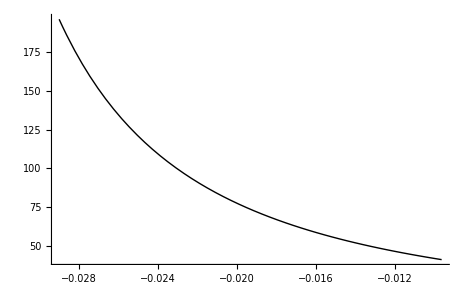

```mathematica
Plot[𝓂E /. ϑ -> ϑPlot,{ϑPlot,ϑMin+0.0001,ϑGIC}]
```

```mathematica
{(ÞΓ^-ρ-1)
(*,(1+℘γ)^-ρ-1*)
,(1-ρ (ÞΓ-1))-1
,(1-ρ (ÞΓ-1)-ρ(-(ρ-1))(ÞΓ-1)^2/2)-1
,(1-ρ (ÞΓ-1)-ρ(-(ρ-1))(ÞΓ-1)^2/2-ρ(-(ρ-1))(-(ρ-2))(ÞΓ-1)^3/6)-1
,(- ρ (ÞΓ-1))} /. ϑ -> {ϑMin,ϑGIC}
```

{{0.0101265,0.030428},{0.0100503,0.0297508},{0.0100755,0.029972},{0.0100755,0.029972},{0.0100503,0.0297508}}

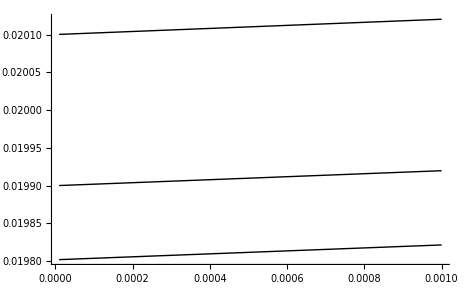

```mathematica
Plot[{
((1+(ÞΓ-1))^-ρ-1),
((1-ρ(ÞΓ-1)-1)),
((1-ρ(ÞΓ-1)-ρ(-(ρ-1)(ÞΓ-1)^2/2)-1))
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All]
```

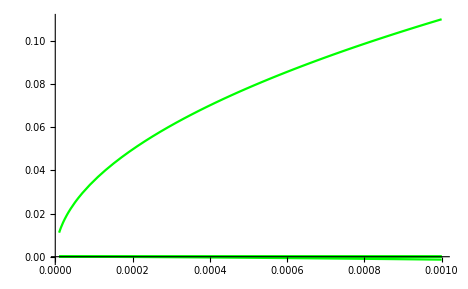

```mathematica
Plot[{
(*Π-((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
,*)
Π-((℧+((1+(ÞΓ-1))^-ρ-1))/℧)^(1/ρ)
,Π-((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
,Π-((1+(ÞΓ^-ρ-1)/℧))^(1/ρ)
,Π-(((ÞΓ^-ρ-1)/℧)(℧/(ÞΓ^-ρ-1)+1))^(1/ρ)
,Π-((ÞΓ^-ρ-1)/℧)^(1/ρ)((℧/(ÞΓ^-ρ-1)+1))^(1/ρ)
,Π-((ÞΓ^-ρ-1)/℧)^(1/ρ)(ρ^-1(℧/(ÞΓ^-ρ-1))+1)
,Π-((ÞΓ^-ρ-1)/℧)^(1/ρ)
(*,
Π-((℧+(1-ρ(ÞΓ-1)-1))/℧)^(1/ρ)*)
(*,Π-(℧+((1-ρ(ÞΓ-1)-ρ(-(ρ-1)(ÞΓ-1)^2/2))-1)/℧)^(1/ρ)*)
(*,Π-((℧+((1+℘γ)^-ρ-1))/℧)^(1/ρ)*)
(*,Π-(((- ρ (ÞΓ-1))+℧)/℧)^(1/ρ)*)
(*,Π-(((- ρ ℘γ)+℧)/℧)^(1/ρ)*)
(*,Π-(((- ρ ℘γ)/℧+1))^(1/ρ)*)
(*,Π-(((- ρ ℘γ)/℧)(1-(℧/( ρ ℘γ))))^(1/ρ)
,Π-((- ρ ℘γ)/℧)^(1/ρ)(1-(℧/( ρ ℘γ)))^(1/ρ)
,Π-((- ρ ℘γ)/℧)^(1/ρ)((1+(1/ρ)(℧/(- ρ ℘γ))))
,Π-((- ρ ℘γ)/℧)^(1/ρ)((1+(1/ρ)(℧/(- ρ ℘γ))+(1/ρ)((1/ρ)-1)(℧/(- ρ ℘γ))^2/2))*)
(*,Π-((- ρ ℘γ)/℧)^(1/ρ)((1-(℧/( ℘γ))))*)
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All,PlotStyle->{Red,Green}]
```

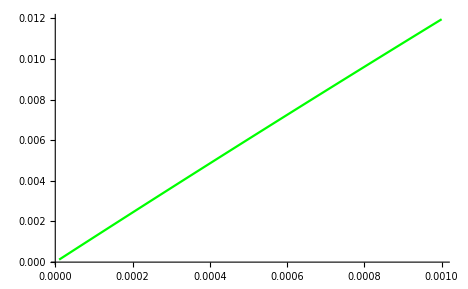

```mathematica
Plot[{
(℧/(ÞΓ^-ρ-1))
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All,PlotStyle->{Red,Green}]
```

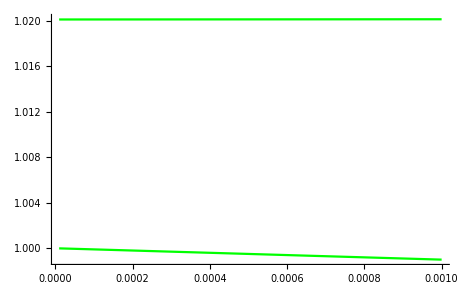

```mathematica
Plot[{
(1-℧)/. ℧ -> ℧Plot
,ÞΓ^-ρ
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All,PlotStyle->{Red,Green}]
```

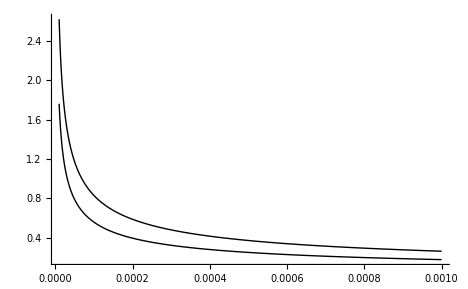

```mathematica
Plot[{
((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
-((℧+(1-ρ(ÞΓ-1)-1))/℧)^(1/ρ),
((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
-((℧-ρ ℘γ)/℧)^(1/ρ)
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All]
```

```mathematica
(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1
```

1.02074

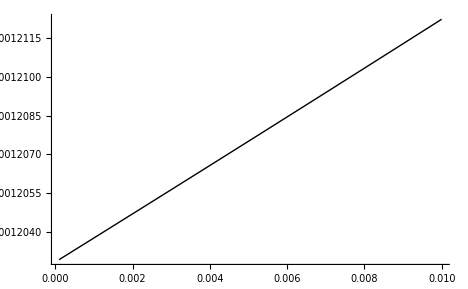

```mathematica
Plot[{℧((1-ÞRtn)((ÞΓ^-ρ-1)/℧)^(1/ρ))^ρ} /. ℧ -> ℧Plot,{℧Plot,0.0001,0.01},PlotRange->All]
```

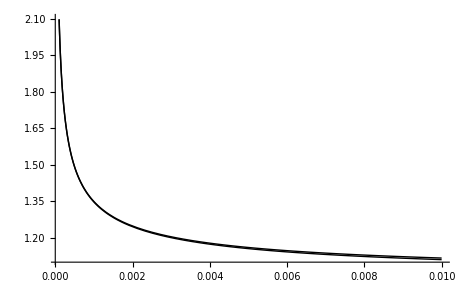

```mathematica
Plot[{(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1
,(1-ÞRtn)((ÞΓ^-ρ-1)/℧)^(1/ρ)+ℛ^-1} /. ℧ -> ℧Plot,{℧Plot,0.0001,0.01},PlotRange->All]
```

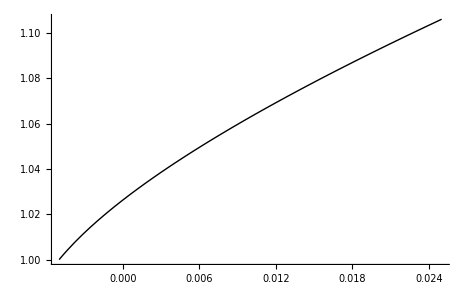

```mathematica
Plot[(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1 /. 𝔤 -> 𝔤Plot,{𝔤Plot,𝔤MinFromGIC,𝔤MaxFromFHWC}]
```

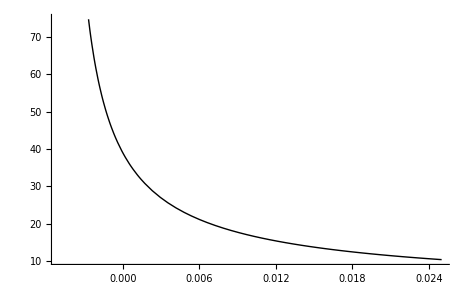

```mathematica
Plot[𝓂E /. 𝔤 -> 𝔤Plot,{𝔤Plot,𝔤MinFromGIC,𝔤MaxFromFHWC}]
```

```mathematica
MatrixForm[{
{1,(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1}
,{1,(1-ÞRtn)((1+(1/ρ)ϖ))+ℛ^-1}
,{1,(1-ÞRtn)((1+(1/ρ)ϖ))+ℛ^-1}
,{1,(1-ÞRtn)+(1-ÞRtn)(1/ρ)ϖ+ℛ^-1}
,{0,-ÞRtn+(1-ÞRtn)(1/ρ)ϖ+ℛ^-1}
,{0,-ÞRtn+κ(1/ρ)ϖ+ℛ^-1}
,{ÞRtn,κ(1/ρ)ϖ+ℛ^-1}
,{ÞRtn,κ(1/ρ)ϖ+ℛ^-1}
,{Þ,κ(1/ρ)ϖ (R)+Γ}
,{Þ,κ(1/ρ)((1-ρ  ℘γ-1)/℧)(R)+Γ}
,{Þ,κ(1/ρ)((-ρ ℘γ)/℧)(R)+Γ}
,{Þ,κ((- ℘γ)/℧)(R)+Γ}
,{ÞΓ,κ((- ℘γ)/℧)ℛ+1}
,{ÞΓ-1,κ((- ℘γ)/℧)ℛ}
,{℘γ,κ((- ℘γ)/℧)ℛ}
} /. 𝔤 -> {𝔤MinFromGIC}]
```

(1 | {1.}
1 | {1.}
1 | {1.}
1 | {1.}
0 | {-1.11022×10^-16}
0 | {-1.11022×10^-16}
0.970874 | {0.970874}
0.970874 | {0.970874}
1. | {1.}
1. | {1.}
1. | {1.}
1. | {1.}
{1.} | {1.}
{-1.11022×10^-16} | {6.66134×10^-16}
{-1.11022×10^-16} | {6.66134×10^-16})

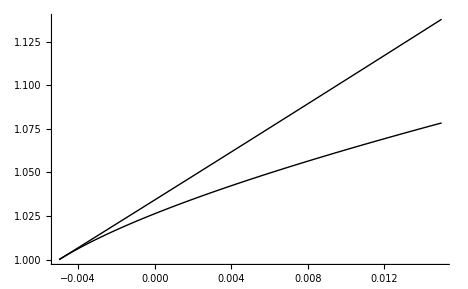

```mathematica
Plot[{(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1 ,(1-ÞRtn)+(1-ÞRtn)(1/ρ)ϖ+ℛ^-1}/. 𝔤 -> 𝔤Plot,{𝔤Plot,𝔤MinFromGIC,𝔤MinFromGIC+0.02}]
```

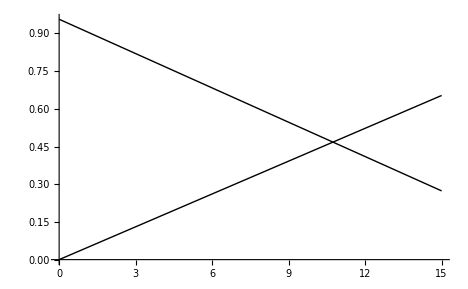

```mathematica
Plot[{((μ-1)/μ)m ,((ℛ^-1-1)/ℛ^-1)m+ℛ^-1 }/. r -> rMaxFromGIC,{m,0,15}]
```

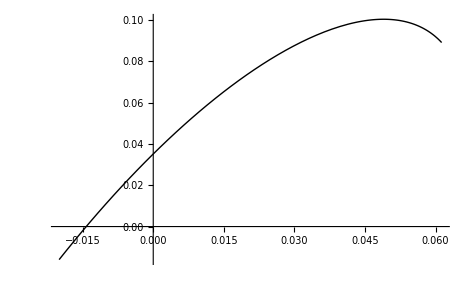

```mathematica
Plot[((μ-1)/μ)-((ℛ^-1-1)/ℛ^-1) /. r -> rPlot,{rPlot,-0.02,rMaxFromGIC}]
```

```mathematica
℧(ρ/(ρ-1))-ϑ/(ρ-1)
```

-0.02

```mathematica
μ
```

1+13.9321 (1+r) √(-0.995+1.06129/(1+r)) (1-0.985329/(√(1+r)))

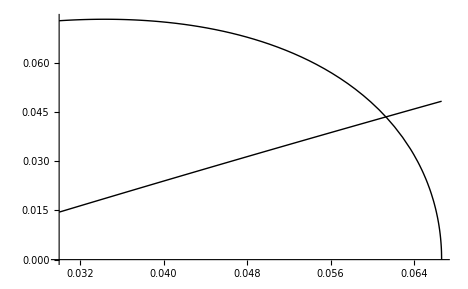

```mathematica
Plot[{(ζ/(1+ζ)),(1-ℛ^-1)} /. r -> rIndex,{rIndex,rMinFromRIC,rMaxFromGIC}]
```

```mathematica
rMaxFromGIC
```

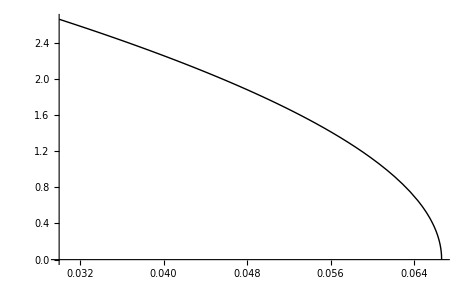

```mathematica
Plot[Π /. r -> rIndex,{rIndex,rMin,rMaxFromGIC}]
```

```mathematica
Π /. r -> rMaxThatGeneratesSS
```

1.

```mathematica
{κ
```

1-0.985329/(√(1+r))

```mathematica
ÞΓ /. r -> rMaxThatGeneratesSS
```

1.

```mathematica
Clear[r];MatrixForm[{{ζ/(1+ζ),">",(1-ℛ^-1)}
,{ℛ ζ/(1+ζ),">",(ℛ-1)}
,{ℛ ((ζ/(1+ζ))-1)+1,">",0}
,{ℛ ((ζ/(1+ζ))-1)+1,">",0}
,{ℛ ((ζ/(1+ζ))-1),">",-1}
,{ℛ (1-(ζ/(1+ζ))),"<",1}
,{ℛ ((1)-(ζ/(1+ζ))),"<",1}
,{ℛ (((1+ζ)/(1+ζ))-(ζ/(1+ζ))),"<",1}
,{ℛ (1/(1+ζ)),"<",1}
,{ℛ ,"<",1+ζ}
,{ℛ ,"<",1+ℛ κ Π }
,{ℛ ,"<",1+ℛ  (1-ÞRtn) Π}
,{ℛ ,"<",1+  (ℛ-ÞΓ) Π}
,{ℛ (1-Π),"<",1 -ÞΓ Π}
}]/. r ->{rMaxThatGeneratesSS-0.001,rMaxThatGeneratesSS+0.001}
```

({0.0467801,0.0398296} | > | {0.0426431,0.0444455}
{0.0488638,0.0416821} | > | {0.0445425,0.0465128}
{0.0043213,-0.00483065} | > | 0
{0.0043213,-0.00483065} | > | 0
{-0.995679,-1.00483} | > | -1
{0.995679,1.00483} | < | 1
{0.995679,1.00483} | < | 1
{0.995679,1.00483} | < | 1
{0.995679,1.00483} | < | 1
{1.04454,1.04651} | < | {1.04908,1.04148}
{1.04454,1.04651} | < | {1.04908,1.04148}
{1.04454,1.04651} | < | {1.04908,1.04148}
{1.04454,1.04651} | < | {1.04908,1.04148}
{-0.0942617,0.103648} | < | {-0.0897283,0.0986165})

```mathematica
(* Successive approximations to Π *)
MatrixForm[{{1,Π-(1+(ÞΓ^-ρ-1)/℧)^(1/ρ)}
,{2,Π-(1+((1+(ÞΓ-1))^-ρ-1)/℧)^(1/ρ)}
,{3,Π-(1+ρ^-1(((1+(ÞΓ-1))^-ρ-1)/℧))}
,{4,Π-(1+ρ^-1(((1-ρ(ÞΓ-1)-ρ(-ρ-1)((ÞΓ-1)^2/2))-1)/℧))}
,{5,Π-(1+ρ^-1(((1-ρ (ρ^-1(r-ϑ)-γ))-1)/℧))}
,{6,Π-(1+ρ^-1(((1- ((r-ϑ)-ρ γ))-1)/℧))}
,{7,Π-(1+ρ^-1((ÞΓ^-ρ-1)/℧)+ρ^-1(ρ^-1-1)((ÞΓ^-ρ-1)/℧)^2/2)}
,{8,Π-(1+ρ^-1(((1-ρ(ÞΓ-1))-1)/℧)+ρ^-1(ρ^-1-1)(((1-ρ(ÞΓ-1))-1)/℧)^2/2)}
,{9,Π-(1+ρ^-1(((1-ρ ℘γ)-1)/℧)+ρ^-1(ρ^-1-1)(((1-ρ ℘γ)-1)/℧)^2/2)}
,{10,Π-(1+ρ^-1(((-ρ ℘γ)/℧)+ρ^-1(ρ^-1-1)(((-ρ ℘γ))/℧)^2/2))}
}
]/. r ->  {rMaxThatGeneratesSS-0.005,rMaxThatGeneratesSS,rMaxThatGeneratesSS+0.005}
```

(1 | {4.44089×10^-16,4.44089×10^-16,1.80411×10^-15}
2 | {4.44089×10^-16,4.44089×10^-16,1.80411×10^-15}
3 | {-0.0781095,4.44089×10^-16,-0.281748}
4 | {-0.0781043,4.44089×10^-16,-0.281754}
5 | {0.0316072,0.136362,-0.114303}
6 | {0.0316072,0.136362,-0.114303}
7 | {0.033923,4.44089×10^-16,-0.171807}
8 | {0.0348059,4.44089×10^-16,-0.169374}
9 | {0.0345118,4.44089×10^-16,-0.170187}
10 | {-0.0212405,4.44089×10^-16,-0.225416})

```mathematica
rHatMaxThatGeneratesSS = rHatFind /.(FindRoot[ℛ (ΠHat-1) -(1-(1+(ρ^-1(r-ϑ)-γ)/℧) ΠHat) /. r -> rHatFind,{rHatFind,rMaxThatGeneratesSS-0.001}]) ;
{rMaxThatGeneratesSS,rHatMaxThatGeneratesSS}
```

{0.0612894,0.0599257}

```mathematica
Clear[r];FindRoot[ℛ(1-ΠHat) -(1-(1+℘γApprox) ΠHat) /. r -> rSeek ,{rSeek,rMaxFromGIC}]
```

{rSeek→0.0599257}

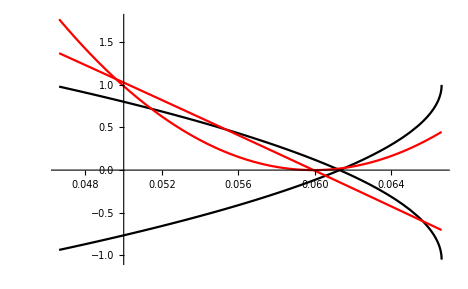

```mathematica
(* Unfortunately, if we go very far from the truth the approximation is poor; actually there are multiple solutions  *)
Plot[{ℛ(Π-1) /. r -> rIndex,1-ÞΓ Π/. r -> rIndex,ℛ (ΠHat-1) /. r -> rIndex, 1-(1+(ρ^-1(r-ϑ)-γ)/℧) ΠHat /. r -> rIndex } ,{rIndex,rMaxFromGIC-0.02,rMaxFromGIC},PlotStyle->{Black,Black,Red,Red}]
```

```mathematica
(* Find the approximate analytical solution *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Get["../../CoreCode/Autoload/init.m"];
Get["../../CoreCode/MakeAnalyticalResults.m"];
Get["../../CoreCode/VarsAndFuncs.m"];
(* Define ΠHat as one of the approximations derived below; needs to be defined here to remain analytical/dynamic *)
℘γApprox=(ρ^-1(r-ϑ)-γ);
Clear[r];(*ΠHat=(1+ρ^-1(((-ρ ℘γ)/℧)));*)
ΠHat=(1- ℘γApprox/℧);
(*ΠHat=(1+ρ^-1(((1-ρ(ÞΓ-1))-1)/℧)+ρ^-1(ρ^-1-1)(((1-ρ(ÞΓ-1))-1)/℧)^2/2);*)
ζHat=ℛ κ ΠHat; 
(* If the starting point is close to the truth, then it finds the right answer *)
```

```mathematica
Clear[r];Solve[ℛ (ΠHat-1)-(1-(1+℘γApprox/℧) ΠHat)==0,{r}]
```

{{r→ϑ+ρ Log[(1+𝔤)/(1-℧)]},{r→(ϑ+𝔤 ϑ-ρ ℧+ρ ℧^2+ρ Log[(1+𝔤)/(1-℧)]+𝔤 ρ Log[(1+𝔤)/(1-℧)])/(1+𝔤+ρ ℧-ρ ℧^2)}}

```mathematica
Severance=PDies=τ=0;𝔤=𝔤Min=0.01;ρ=ρBase=2;ϑ=ϑBase=0.03;℧=℧Base=0.005;𝔤Gap=0.01;
rMinFromFHWC=𝔤Min + ℧;
rMinFromRIC=ϑ/(ρ-1);
rMin=Max[rMinFromFHWC,rMinFromRIC];
rMaxFromGICApprox=ρ 𝔤Min + ℧(ρ+1)+ϑ;
rMaxFromGIC=𝔊^ρ/(β(1-℧)^(ρ+1))-1;
(* For any r greater than this, no SS exists *)
rMaxThatGeneratesSS = rFind /.(FindRoot[ ζ/(1+ζ) - (1-ℛ^-1) /. r -> rFind,{rFind,rMin+0.001}]) ;
{rMaxFromGICApprox,rMaxFromGIC,rMaxThatGeneratesSS};Solve[ℛ (ΠHat-1)-(1-(1+℘γApprox/℧) ΠHat)==0,{r}]
```

{{r→0.0495858},{r→0.0599257}}

```mathematica
{ρ^-1(r-ϑ)-(𝔤+℧)<ρ^-1℧
,(r-ϑ)<℧+ρ(𝔤+℧)
,r<ϑ + ℧(ρ+1)+ρ 𝔤
,(ρ^-1(r-ϑ)-r)<0
,r (ρ^-1-1)-ϑ ρ^-1<0
,r ρ^-1(1-ρ)<ϑ ρ^-1
,r (1-ρ)-ϑ<0
,r (ρ-1)+ϑ >0
,r (ρ-1)>-ϑ
,r>𝔤}

{-0.015+1/2 (-0.03+r)<0.0025,-0.03+r<0.034999999999999996,r<0.065,1/2 (-0.03+r)-r<0,-0.015-r/2<0,-r/2<0.015,-0.03-r<0,0.03+r>0,r>-0.03,r>0.01}
{(((R) β)^(1/ρ))/(𝔊/(1-℧))<(1-℧)^(-1/ρ)
,
(((R) β)^(1/ρ))(1-℧)/𝔊<(1-℧)^(-1/ρ)
,
(((R) β)^(1/ρ))(1-℧)^(1+1/ρ)/𝔊<1
,
(((R) β)^(1/ρ))(1-℧)^((ρ+1)/ρ)𝔊^-1<1
,
((R) β)(1-℧)^(ρ+1)𝔊^-ρ<1
,
((R) β)<𝔊^ρ(1-℧)^(-(ρ+1))
,
(R) <𝔊^ρ/(β(1-℧)^(ρ+1))
}

{True,True,True,True,True,True,True}
```

```mathematica
MatrixForm[{{ζ/(1+ζ),(1-ℛ^-1)}
,{ζ/(1+ζ),(ℛ-1)/ℛ}
,{ℛ ζ,(1+ζ)(ℛ-1)}
,{ℛ ζ,(1+ζ)(ℛ-1)}
,{ℛ ζ,ℛ + ℛ ζ-(1+ζ)}
,{0,ℛ -(1+ζ)}
,{(1+ζ),ℛ }
,{1+ℛ (1-ÞRtn)Π,ℛ }
,{1+ℛ (1-ÞRtn)Π,ℛ }
}]/. r -> rMaxThatGeneratesSS-0.01
```

(0.0643932 | 0.0344472
0.0643932 | 0.0344472
0.0712804 | 0.0381316
0.0712804 | 0.0381316
0.0712804 | 0.0381316
0 | -0.0331489
1.06883 | 1.03568
1.06883 | 1.03568
1.06883 | 1.03568)

```mathematica
Π /. r -> rMax
```

14.1421 √(-0.995+1.06129/(1+r))